# Exploration of Tanzania (Nyakatoke) village risk sharing network structure

Villagers in Nyakatoke were asked to list people who they could ask for assistance, or who could ask them for assistance, when faced with financial difficulties  In the reported data, sometimes both households list the other, and sometimes only one lists the other.  We create three networks from this graph:

An undirected graph where we assume that links are underreported.  If either Household says there is a link with the other, we insert the corresponding edge in the graph

An undirected graph where we assume that links are overreported.  We require both households to report the link before we insert the corresponding edge in the graph

A directed graph where we assume that a household listing another household means they wish (desire) for a link between the households exist.  No actual link may exist.  Since thse desires might not be symmteric, the graph is directed.

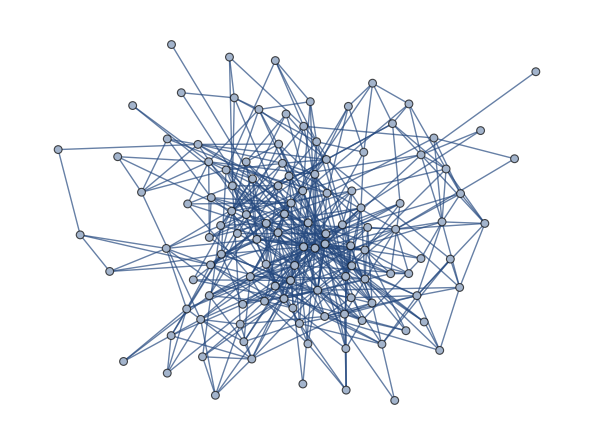

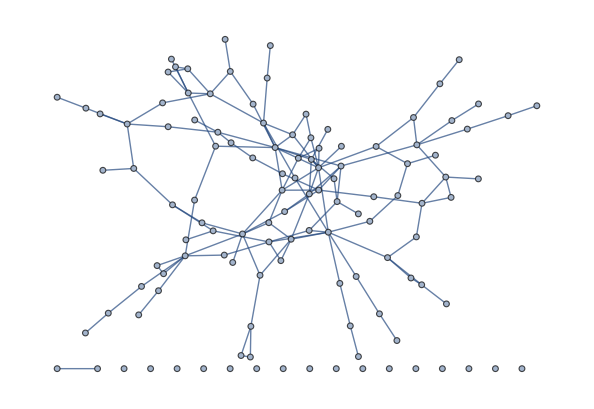

-Graphics-

```mathematica
underReportingGraph = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data","underreporting_model.graphml"}]]
overReportingGraph = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"data","overreporting_model.graphml"}]]
desireToLinkGraph = Import[FileNameJoin[{ParentDirectory[NotebookDirectory[]], "data", "desire_to_link_model.graphml"}]]
```

## Basic Statistics

```mathematica
sizeUnderReporting = EdgeCount[underReportingGraph]
sizeOverReporting = EdgeCount[overReportingGraph]
sizeDesireToLink = EdgeCount[desireToLinkGraph]
```

490

140

630

```mathematica
orderUnderReporting = VertexCount[underReportingGraph]
orderOverReporting = VertexCount[overReportingGraph]
orderDesireToLink = VertexCount[desireToLinkGraph]
```

119

119

119

```mathematica
clusteringCoefficientUnderReporting = GlobalClusteringCoefficient[underReportingGraph]
clusteringCoefficientOverReporting = GlobalClusteringCoefficient[overReportingGraph]
clusteringCoefficientDesireToLink = GlobalClusteringCoefficient[desireToLinkGraph]
clusteringCoefficientDesireToLinkAsUndirected = GlobalClusteringCoefficient[UndirectedGraph[desireToLinkGraph]]
```

189/1003

33/410

129/1274

189/1003

```mathematica
avgClusteringUnderReporting = MeanClusteringCoefficient[underReportingGraph]
avgClusteringOverReporting = MeanClusteringCoefficient[overReportingGraph]
avgClusteringDesireToLink = MeanClusteringCoefficient[desireToLinkGraph]
avgClusteringDesireToLinkAsUndirected = MeanClusteringCoefficient[UndirectedGraph[desireToLinkGraph]]
```

102131927129/438927785296

2299/29988

213243970651810993820440133648/1867895371408044552144806460225

102131927129/438927785296

```mathematica
dUnderReporting = GraphDiameter[underReportingGraph]
dOverReporting = GraphDiameter[overReportingGraph]
dDesireToLink = GraphDiameter[desireToLinkGraph]
```

5

∞

∞

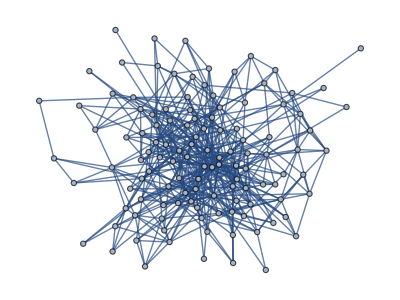

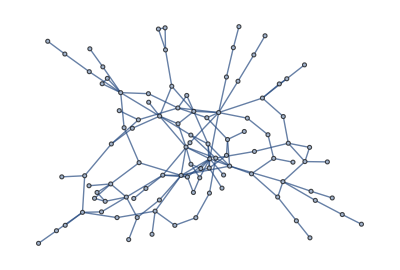

-Graphics-

```mathematica
giantComponentUnderReporting = ConnectedComponents[underReportingGraph]//First // Subgraph[underReportingGraph, #]&
giantComponentOverReporting = ConnectedComponents[overReportingGraph] // First // Subgraph[overReportingGraph, #] &
giantComponentDesireToLink = WeaklyConnectedComponents[desireToLinkGraph] // First // Subgraph[desireToLinkGraph, #]&
```

```mathematica
aplUnderReporting = MeanGraphDistance[giantComponentUnderReporting]
aplOverReporting = MeanGraphDistance[giantComponentOverReporting]
aplDesireToLink = MeanGraphDistance[giantComponentDesireToLink]
```

17994/7021

12109/2525

∞

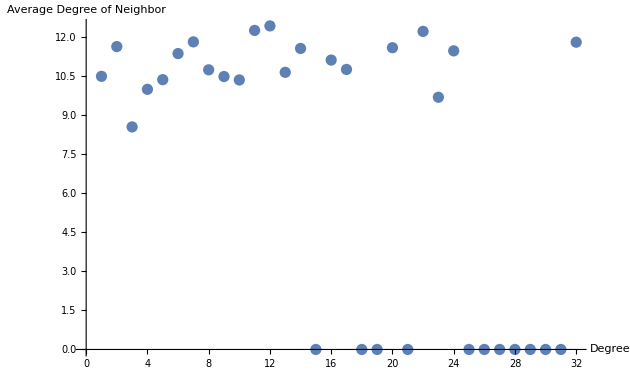

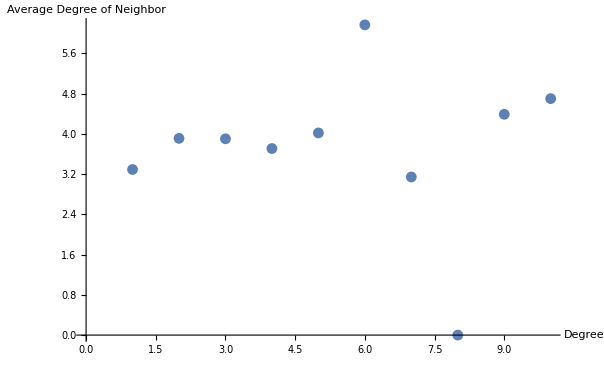

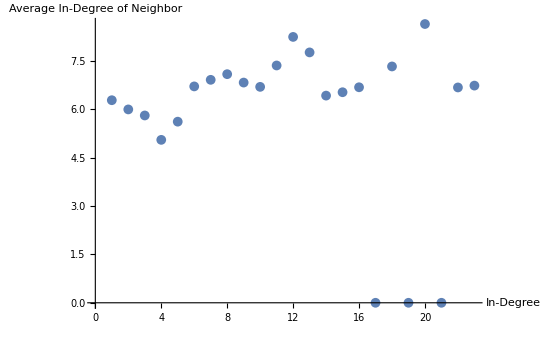

0.0332259

0.0857553

0.0672929

```mathematica
ListPlot[Rest[MeanDegreeConnectivity[underReportingGraph]],AxesLabel->{"Degree", "Average Degree of Neighbor"}]
ListPlot[Rest[MeanDegreeConnectivity[overReportingGraph]], AxesLabel->{"Degree", "Average Degree of Neighbor"}]
ListPlot[Rest[MeanDegreeConnectivity[desireToLinkGraph, "In"]], AxesLabel->{"In-Degree", "Average In-Degree of Neighbor"}]
N[GraphAssortativity[underReportingGraph]]
N[GraphAssortativity[overReportingGraph]]
N[GraphAssortativity[desireToLinkGraph]]
```

```mathematica
N[10223/(8 √360610651)]
```

0.0672929

## Simulations

```mathematica
(*underReportingER = RandomGraph[UniformGraphDistribution[orderUnderReporting, sizeUnderReporting], 100000];
overReportingER = RandomGraph[UniformGraphDistribution[orderOverReporting, sizeOverReporting], 100000];
desireToLinkER= RandomGraph[UniformGraphDistribution[orderDesireToLink, sizeDesireToLink], 100000, DirectedEdges->True]; *)
```

```mathematica
(*underReportingConfig = RandomGraph[DegreeGraphDistribution[VertexDegree[underReportingGraph]], 100000];
overReportingConfig = RandomGraph[DegreeGraphDistribution[VertexDegree[overReportingGraph]], 100000];
desireToLinkConfig = RandomGraph[DegreeGraphDistribution[VertexInDegree[desireToLinkGraph]], 100000, DirectedEdges->True];*)
```

### Clustering

#### Erdos-Renyi

```mathematica
(*erSimUnderReportingClusteringCoefficientMean = Mean[Map[GlobalClusteringCoefficient, underReportingER]];
erSimOverReportingClusteringCoefficientMean = Mean[Map[GlobalClusteringCoefficient, overReportingER]];
erSimDesireToLinkClusteringCoefficientMean = Mean[Map[GlobalClusteringCoefficient, desireToLinkER]];*)
```

```mathematica
(*erSimUnderReportingClusteringCoefficientSD = StandardDeviation[Map[GlobalClusteringCoefficient, underReportingER]];
erSimOverReportingClusteringCoefficientSD = StandardDeviation[Map[GlobalClusteringCoefficient, overReportingER]];
erSimDesireToLinkClusteringCoefficientSD = StandardDeviation[Map[GlobalClusteringCoefficient, desireToLinkER]];*)
```

#### Configuration

```mathematica
(*configSimUnderReportingClusteringCoefficientMean = Mean[Map[GlobalClusteringCoefficient, underReportingConfig]];
configSimOverReportingClusteringCoefficientMean =  Mean[Map[GlobalClusteringCoefficient, overReportingConfig]];
configSimDesireToLinkClusteringCoefficientMean = Mean[Map[GlobalClusteringCoefficient, desireToLinkConfig]];*)
```

```mathematica
(*configSimUnderReportingClusteringCoefficientSD = StandardDeviation[Map[GlobalClusteringCoefficient, underReportingConfig]];
configSimOverReportingClusteringCoefficientSD =  StandardDeviation[Map[GlobalClusteringCoefficient, overReportingConfig]];
configSimDesireToLinkClusteringCoefficientSD = StandardDeviation[Map[GlobalClusteringCoefficient, desireToLinkConfig]];*)
```

### Diameter

#### Erdos-Renyi

```mathematica
(*erSimUnderReportingDiameterMean = Mean[Map[GraphDiameter, underReportingER]];
erSimOverReportingDiameterMean = Mean[Map[GraphDiameter, underReportingER]];
erSimDesireToLinkDiameterMean = Mean[ap[GraphDiameter, underReportingER]];*)
```

```mathematica
(*erSimUnderReportingDiameterSD = StandardDeviation[Map[GraphDiameter, underReportingER]];
erSimOverReprtingDiameterSD = StandardDeviation[Map[GraphDiameter, underReportingER]];
erSimDesireToLinkDiameterSD = StandardDeviation[Map[GraphDiameter, underReportingER]];*)
```

#### Configuration

```mathematica
(*configSimUnderReportingDiameterMean= Map[GraphDiameter, underReportingConfig]//Mean;
configSimOverReportingDiameterMean = Map[GraphDiameter, overReportingConfig]//Mean;
configSimesireToLinkDiameterMean = Map[GraphDiameter, desireToLinkConfig]//Mean;*)
```

```mathematica
(*configSimUnderReportingDiameterSD = Map[GraphDiameter, underReportingConfig] // StandardDeviation;
configSimOverReprtingDiameterSD = Map[GraphDiameter, overReportingConfig] // StandardDeviation;
configSimDesireToLinkDiameterSD = Map[GraphDiameter, desireToLinkConfig] // StandardDeviation;*)
```

### Average Path Length

#### Erdos-Renyi

```mathematica
(*erSimUnderReportingAplMean = Map[MeanGraphDistance, underReportingER]//Mean;
erSimOverReportingAplMean = Map[MeanGraphDistance, overReportingER]//Mean;
erSimDesireToLinkAplMean = Map[MeanGraphDistance, desireToLinkER]//Mean;
```

```mathematica
(*erSimUnderReportingAplSD = Map[MeanGraphDistance, underReportingER]//StandardDeviation;
erSimOverReprtingAplSD = Map[MeanGraphDistance, overReportingConfig]//StandardDeviation;
erSimDesireToLinkAplSD = Map[MeanGraphDistance, desireToLinkER]//StandardDeviation;*)
```

#### Configuration

```mathematica
(*configSimUnderReportingAplMean = Map[MeanGraphDistance, underReportingConfig]//Mean;
configSimOverReportingAplMean = Map[MeanGraphDistance, overReportingConfig]//Mean;
configSimesireToLinkAplMean = Map[MeanGraphDistance, desireToLinkConfig]//Mean;*)
```

```mathematica
(*configSimUnderReportingAplSD = Map[MeanGraphDistance, underReportingConfig]//StandardDeviation;
configSimOverReprtingAplSD = Map[MeanGraphDistance, overReportingConfig]//StandardDeviation;
configSimDesireToLinkAplSD = Map[MeanGraphDistance, desireToLinkConfig]//StandardDeviation;*)
```

## Patterns of clustering

{11,7,6,8,4,4,2,11,4,23,6,6,7,8,6,3,24,9,11,12,16,12,14,8,5,10,4,11,24,4,17,7,10,11,7,2,6,12,11,8,10,10,7,10,9,7,4,9,8,5,6,5,8,20,12,10,12,32,7,11,12,8,5,11,4,5,6,2,7,11,10,13,5,13,8,11,4,7,6,3,8,4,5,4,2,10,5,7,6,7,1,5,4,9,6,2,10,7,5,12,8,5,7,6,9,9,1,22,11,2,9,10,6,12,5,5,2,5,3}

{4/11,2/7,4/15,5/28,1/2,2/3,0,2/11,1/2,30/253,2/15,4/15,3/7,1/4,2/15,1/3,19/138,1/6,8/55,3/11,13/120,5/22,19/91,2/7,4/5,1/3,0,18/55,43/276,1/6,11/68,1/7,8/45,6/55,1/7,0,2/15,5/33,9/55,3/14,2/15,2/9,4/21,2/9,1/12,1/21,1/6,1/6,1/14,1/10,7/15,1/2,5/28,13/95,1/6,1/15,19/66,75/496,5/21,16/55,5/33,1/7,3/5,19/55,1/6,2/5,1/15,1,1/3,13/55,8/45,1/6,3/10,7/78,2/7,9/55,1/3,2/21,7/15,1/3,1/7,1/3,1/10,1/6,0,4/15,1/2,5/21,1/3,11/21,0,2/5,0,7/36,1/3,0,1/5,3/7,2/5,8/33,1/14,1/5,5/21,4/15,5/36,1/9,0,38/231,8/55,0,1/6,7/45,2/5,7/33,3/10,1/2,0,2/5,1/3}

-0.182475

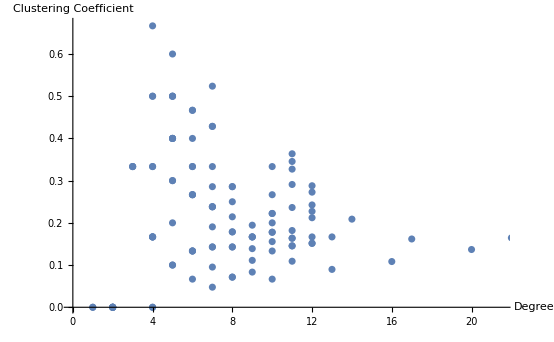

```mathematica
xx = VertexDegree[underReportingGraph]
yy = LocalClusteringCoefficient[underReportingGraph]
N[Correlation[xx, yy]]
data = Transpose@{xx,yy};
ListPlot[data, AxesLabel->{"Degree", "Clustering Coefficient"}]
```

{3,2,2,3,2,2,0,2,2,9,1,2,2,1,2,1,6,2,3,5,1,1,2,2,2,7,3,4,10,0,2,0,4,3,5,0,2,1,1,2,2,3,1,0,5,3,1,2,2,2,3,3,1,5,2,3,5,9,1,3,4,1,2,5,0,1,1,1,2,5,4,3,1,5,2,5,2,2,2,1,2,1,2,0,2,2,2,0,1,4,0,4,1,2,2,0,3,1,3,2,3,2,5,2,3,2,0,7,1,0,3,2,1,5,1,0,0,0,0}

{1/3,0,0,1/3,1,1,0,0,0,1/36,0,0,0,0,0,0,2/15,0,0,1/10,0,0,0,1,1,1/21,0,1/3,4/45,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/10,0,0,0,1/9,0,0,0,0,0,1/5,0,0,0,0,0,0,1/6,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/6,0,1/6,0,0,0,0,0,0,1/3,0,0,1,1/10,0,1/3,0,0,1/21,0,0,0,0,0,0,0,0,0,0,0}

0.076883

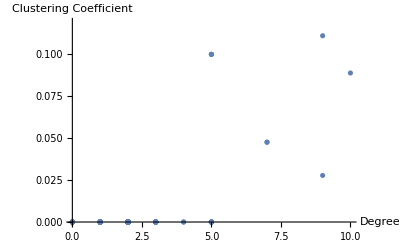

```mathematica
xx = VertexDegree[overReportingGraph]
yy = LocalClusteringCoefficient[overReportingGraph]
N[Correlation[xx, yy]]
data = Transpose@{xx,yy};
ListPlot[data, AxesLabel->{"Degree", "Clustering Coefficient"}]
```

{9,3,4,3,3,2,0,5,2,16,6,4,6,1,3,2,23,8,7,10,14,6,5,3,3,8,4,8,16,4,15,3,6,9,7,0,6,6,8,5,6,7,3,0,9,6,1,5,5,4,6,3,4,18,3,6,10,22,4,4,9,2,2,7,1,3,1,1,4,6,9,12,4,13,5,6,2,4,2,1,4,2,4,0,2,9,5,4,3,4,1,5,3,3,4,0,5,2,4,6,7,4,5,3,7,3,0,20,7,0,6,10,2,11,2,0,0,0,0}

{3/14,1/16,1/14,1/7,2/7,1/3,0,1/38,1/3,11/247,0,0,5/16,1/7,0,1/3,21/155,1/22,5/46,7/65,0,2/41,4/53,5/19,1/2,12/65,0,1/4,14/139,0,3/29,1/6,1/11,1/42,1/15,0,1/10,2/41,1/31,1/23,3/34,5/39,1/14,0,1/20,1/21,0,1/28,0,1/10,2/5,5/12,2/19,10/121,3/31,0,11/65,37/409,0,4/37,3/59,0,3/8,15/58,0,1/8,0,1,1/6,7/55,6/41,1/15,1/7,1/60,5/23,3/55,1/3,1/18,2/5,0,1/22,1/5,0,0,0,2/25,3/8,1/12,0,5/24,0,1/4,0,3/22,1/7,0,1/37,2/11,3/13,4/23,1/25,1/5,2/15,0,1/8,1/22,0,14/173,1/17,0,4/33,0,1/9,4/61,1/7,0,0,0,0}

-0.0650646

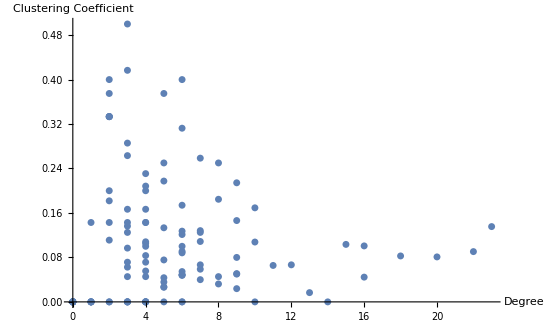

```mathematica
xx = VertexInDegree[desireToLinkGraph]
yy = LocalClusteringCoefficient[desireToLinkGraph]
N[Correlation[xx, yy]]
data = Transpose@{xx,yy};
ListPlot[data, AxesLabel->{"Degree", "Clustering Coefficient"}]
```